# Neural Networks 101

-Graphics-

## Learning Objectives

### What Are Neural Networks?

What Are Neural Networks?

Network Structure: Data, Encoders/Decoders, Layers, Stacking Layers: Network Constructors

Network Training: Theory of Training

Classification Net: Perceptron Model

Convolution Net: LeNet on MNIST Data

## Why Use Neural Networks?

“It [AI] would take off on its own and redesign itself at an ever increasing rate. Humans, who are limited by slow biological evolution, couldn’t compete and would be superseded.”—Stephen Hawking

-Graphics-

If you have not used machine learning, deep learning and neural networks yourself, you have almost certainly heard of them. They are everywhere. You may be familiar with their commercial use in self-driving cars, image recognition, automatic text completion, text translation and other complex data analysis, but you can also train your own neural nets to accomplish tasks like identifying objects in images, generating sequences of text or segmenting pixels of an image.

With the Wolfram Language™, you can get started with machine learning and neural nets faster than you think. Since deep learning, AKA neural networks, is everywhere, this class will explore what exactly neural networks are and how you can start using them.

### Image Classification

```mathematica
net=NetModel["Inception V3 Trained on ImageNet Competition Data"]
```

NetChain[<>]

```mathematica
image=-Graphics-;
```

```mathematica
net[image]
```

Labrador retriever

## What Are Neural Networks?

Neural networks are a programming approach that is inspired by the neurons in the human brain and enables computers to learn from observational data: be it images, audio, text, labels, strings or numbers. They try to model some unknown function (for example,  f: P → Q) that maps this data into numbers or classes by recognizing patterns in the data. They are built from these components:

Encoders and decoders (to convert the input data type to numeric tensors)

Layers (to perform operations on these tensors depending on the applications)

Containers (to hold these operations in a sensible way)

## Network Data: Tensors

### Ranks of Tensors

Tensors are multidimensional arrays.

Rank 0 (scalars): 0.0

Rank 1 (vectors): {0.0, 1.0}

Rank 2 (matrices): {{1., 2., 3.} , {3., 2., 1.}}

Rank n tensors: {... {... {1., 2., 3.}...}...}

### Examples of Tensors

Vectors as coordinates of points

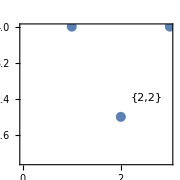
-Graphics-  ≈ ( | 1 |  | 4 | )
( | 3 |  | 4 | )
( | 2 |  | 2 | )

```mathematica
data={{1,4},{3,4},{2,2}};
plot=ListPlot[Labeled[#,Framed[#,FrameStyle->None]]&/@data,Frame->True,LabelStyle->Medium,AspectRatio->1,PlotRangePadding->1,PlotStyle->PointSize[0.04],ImageSize->Small];
gr=Grid[{{Style["(",20],Style[1,20],Spacer[1],Style[4,20],Style[")",20]},{Style["(",20],Style[3,20],Spacer[1],Style[4,20],Style[")",20]},{Style["(",20],Style[2,20],Spacer[1],Style[2,20],Style[")",20]}}];Row[{plot, Spacer[60], Style["  ≈ ",32], Spacer[60], gr}]
```

Matrices as grayscale images

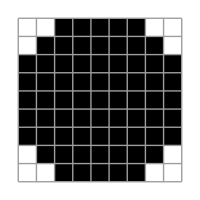
-Graphics-  ≈ (0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0)

```mathematica
Row[{ArrayPlot[DiskMatrix[4],Mesh->All,ImageSize->200], Spacer[60], Style["  ≈ ",32], Spacer[60], MatrixForm@DiskMatrix[4]}]
```

Rank-3 tensors as colored images

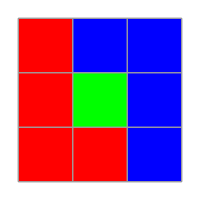
-Graphics-  ≈ ((1 | 0 | 0
1 | 0 | 0
1 | 1 | 0) | (0 | 0 | 0
0 | 1 | 0
0 | 0 | 0) | (0 | 1 | 1
0 | 0 | 1
0 | 0 | 1))

```mathematica
re={1,0,0};bl={0,0,1};gr={0,1,0};data={{re,bl,bl},{re,gr,bl},{re,re,bl}};img=Image[data];Row[{ArrayPlot[ImageData@img,ColorFunction->RGBColor,Mesh->True,ImageSize->200], Spacer[60], Style["  ≈ ",32], Spacer[60],MatrixForm[{MatrixForm/@Round[Transpose[data,{2,3,1}]]}]}]
```

## NetEncoders: Class

NetEncoder is used to convert any data received to an input tensor. Similarly, after the optimization (training) has been done, the output tensor is converted to the data format using NetDecoder.

#### Class encoders and decoders

Encode the user-defined class (here the class of male and females):

```mathematica
enc=NetEncoder[{"Class",{"male","female"}}]
```

NetEncoder[<>]

Use it to create the input tensor:

```mathematica
enc[{"male","female","female"}]
```

{1,2,2}

Create the decoder for the same classes:

```mathematica
dec=NetDecoder[{"Class",{"male","female"}}]
```

NetDecoder[<>]

Use a probabilistic approach to decode the output (make sure each of the tensors to be decoded follows the dimension specification of the decoder):

```mathematica
dec[{{0.1,0.9},{0.7,0.3},{0.8,0.2}}]
```

{female,male,male}

## NetEncoders: Image

#### Image encoder

```mathematica
image= -Graphics-;
```

```mathematica
ImageDimensions@image
```

{236,213}

```mathematica
enc=NetEncoder[{"Image",ImageDimensions[image],ColorSpace->"Grayscale"}]
```

NetEncoder[<>]

```mathematica
encoded=enc[image]
```

{{{0.341176,0.345098,0.345098,0.34902,0.352941,226,0.243137,0.235294,0.235294,0.235294,0.235294},211,{1}}}
 |  |  |  |

```mathematica
Dimensions@encoded
```

{1,213,236}

```mathematica
netchar=NetEncoder["Characters"]
```

NetEncoder[<>]

```mathematica
netchar["hello world"]
```

{75,72,79,79,82,3,90,82,85,79,71}

```mathematica
Dimensions@encoded
```

{1,213,236}

```mathematica
dec=NetDecoder[{"Image",ColorSpace->"Grayscale"}]
```

NetDecoder[<>]

```mathematica
dec[encoded]
```

-Graphics-

## Exploration: Create Your Own Encoder

Background

NetEncoder["Characters"] is suitable for typical English prose and consists of all printable ASCII characters, as well as tab, space and newline. So it has a list of the following characters: {"	","
",FromCharacterCode[Range[32,126]]}.
But what if you have a piece of text that has characters outside this range?

Obtain the character encoder and evaluate it on an example outside the FromCharacterCode range, say on the following string “Zervynų-Miškas”:

```mathematica
enc=NetEncoder["Characters"]
```

NetEncoder[<>]

```mathematica
enc["Zervynų-Miškas"]
```

NetEncoder::invencin: Invalid input, input string contained unkown characters and the encoder doesn't contain _ in the character list.

$Failed

One way to solve this problem is to create an encoder that assigns unknown characters to a special code along with the 97 characters:

```mathematica
enc=NetEncoder[{"Characters",{Automatic,_}}]
```

NetEncoder[<>]

```mathematica
enc["Zervynų-Miškas"]
```

{61,72,85,89,92,81,98,16,48,76,98,78,68,86}

So here 98 will be the unknown character, and any time you find a character outside the vocabulary, it will assign an unknown token. But can you guess the problem in such cases?

The other way is to create a custom encoder with a “richer vocabulary”, to circumvent the problem of assigning the same token to all unknowns. This could be customized to your problem. For this problem, obtain all the forest names from the rich entity store in the Wolfram Language:

```mathematica
EntityValue[EntityList["Forest"],"Name"]
```

{2 M Corazon,A B Williams Memorial Woods,A la Fange Gros Jean,Aachener Stadtforst,Aaïz Qâni,Aandankulam,Aarberg,20242,Zweibrunnhau,Zwenzower Tannen,Zwerchecker-Wald,Zwethauer Wald,Zwölf Pfarren-Wald,Zwölfer Holz}
 |  |  |  |

```mathematica
forestNames=DeleteMissing@EntityValue[EntityList["Forest"],"Name"];
```

Perform a little bit of string manipulation to replace the spaces with a "-":

```mathematica
forestNames=StringReplace[forestNames,{" " -> "-"} ];
```

Create a vocabulary with all occurring characters and list them:

```mathematica
str=StringJoin@forestNames;vocab=FromCharacterCode/@Sort@ToCharacterCode[Keys@CharacterCounts[str]]
```

{&,',,,-,.,/,0,1,2,3,4,5,6,8,9,A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z,a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,Á,Ä,Å,Ç,É,Î,Ð,Ö,Ø,Ü,Þ,ß,à,á,â,ã,ä,å,æ,ç,è,é,ê,ë,í,î,ï,ð,ñ,ó,ô,ö,ø,ú,û,ü,ý,Ā,ā,ă,ą,ć,Č,č,đ,ē,ė,ę,ě,ğ,Ģ,Ī,ī,İ,ı,ķ,ļ,Ł,ł,ń,ņ,ň,Ō,ō,ő,ř,Ś,ś,ş,Š,š,Ţ,ţ,Ū,ū,ů,ű,ų,ź,Ż,ż,Ž,ž,ơ,̧,Ḑ,ḑ,Ḩ,ḩ,ẕ,ừ,‘,’}

Now create a NetEncoder with your customized vocabulary:

```mathematica
newEnc=NetEncoder[{"Characters",{vocab,_ }}]
```

NetEncoder[<>]

Evaluate your encoder on the original example “Zervynų-Miškas”:

```mathematica
newEnc["Zervynų-Miškas"]
```

{41,46,59,63,66,55,145,4,28,50,138,52,42,60}

## Layers

A neural network is a biologically inspired model and consists of “layers” or “neurons” through which information is processed from the input to the output tensor. Layers are usually defined by their mathematical operation.

The following figure shows a simple construction of a feed-forward neural network:

-Graphics-

Source: http://cs231n.github.io/neural-networks-1

The implemented layers in the Wolfram Language are:

```mathematica
{{Layer Type, Layers}, {Basic Layers, LinearLayerhttps://reference.wolfram.com/language/ref/LinearLayer.htmlNonehttps://reference.wolfram.com/language/ref/LinearLayer.htmlHyperlinkHyperlinkActive|ElementwiseLayerhttps://reference.wolfram.com/language/ref/ElementwiseLayer.htmlNonehttps://reference.wolfram.com/language/ref/ElementwiseLayer.htmlHyperlinkHyperlinkActive|SoftmaxLayerhttps://reference.wolfram.com/language/ref/SoftmaxLayer.htmlNonehttps://reference.wolfram.com/language/ref/SoftmaxLayer.htmlHyperlinkHyperlinkActive}, {Computation Elementwise Layers, ElementwiseLayerhttps://reference.wolfram.com/language/ref/ElementwiseLayer.htmlNonehttps://reference.wolfram.com/language/ref/ElementwiseLayer.htmlHyperlinkHyperlinkActive|ThreadingLayerhttps://reference.wolfram.com/language/ref/ThreadingLayer.htmlNonehttps://reference.wolfram.com/language/ref/ThreadingLayer.htmlHyperlinkHyperlinkActive|ConstantTimesLayerhttps://reference.wolfram.com/language/ref/ConstantTimesLayer.htmlNonehttps://reference.wolfram.com/language/ref/ConstantTimesLayer.htmlHyperlinkHyperlinkActive|ConstantPlusPlayerhttps://reference.wolfram.com/language/ref/ConstantPlusLayer.htmlNonehttps://reference.wolfram.com/language/ref/ConstantPlusLayer.htmlHyperlinkHyperlinkActive}, {Convolution Filtering Layers, ConvolutionLayerhttps://reference.wolfram.com/language/ref/ConvolutionLayer.htmlNonehttps://reference.wolfram.com/language/ref/ConvolutionLayer.htmlHyperlinkHyperlinkActive|DeconvolutionLayerhttps://reference.wolfram.com/language/ref/DeconvolutionLayer.htmlNonehttps://reference.wolfram.com/language/ref/DeconvolutionLayer.htmlHyperlinkHyperlinkActive|PoolingLayerhttps://reference.wolfram.com/language/ref/PoolingLayer.htmlNonehttps://reference.wolfram.com/language/ref/PoolingLayer.htmlHyperlinkHyperlinkActive|ResizeLayerhttps://reference.wolfram.com/language/ref/ResizeLayer.htmlNonehttps://reference.wolfram.com/language/ref/ResizeLayer.htmlHyperlinkHyperlinkActive|SpatialTransformationLayerhttps://reference.wolfram.com/language/ref/SpatialTransformationLayer.htmlNonehttps://reference.wolfram.com/language/ref/SpatialTransformationLayer.htmlHyperlinkHyperlinkActive}, {Layers Optimization Training, ImageAugmentationLayerhttps://reference.wolfram.com/language/ref/ImageAugmentationLayer.htmlNonehttps://reference.wolfram.com/language/ref/ImageAugmentationLayer.htmlHyperlinkHyperlinkActive|BatchNormalizationLayerhttps://reference.wolfram.com/language/ref/BatchNormalizationLayer.htmlNonehttps://reference.wolfram.com/language/ref/BatchNormalizationLayer.htmlHyperlinkHyperlinkActive|DropoutLayerhttps://reference.wolfram.com/language/ref/DropoutLayer.htmlNonehttps://reference.wolfram.com/language/ref/DropoutLayer.htmlHyperlinkHyperlinkActive|LocalResponseNormalizationLayerhttps://reference.wolfram.com/language/ref/LocalResponseNormalizationLayer.htmlNonehttps://reference.wolfram.com/language/ref/LocalResponseNormalizationLayer.htmlHyperlinkHyperlinkActive|NormalizationLayerhttps://reference.wolfram.com/language/ref/NormalizationLayer.htmlNonehttps://reference.wolfram.com/language/ref/NormalizationLayer.htmlHyperlinkHyperlinkActive}, {Layers Manipulation Structure, CatenateLayerhttps://reference.wolfram.com/language/ref/CatenateLayer.htmlNonehttps://reference.wolfram.com/language/ref/CatenateLayer.htmlHyperlinkHyperlinkActive|FlattenLayerhttps://reference.wolfram.com/language/ref/FlattenLayer.htmlNonehttps://reference.wolfram.com/language/ref/FlattenLayer.htmlHyperlinkHyperlinkActive|ReshapeLayerhttps://reference.wolfram.com/language/ref/ReshapeLayer.htmlNonehttps://reference.wolfram.com/language/ref/ReshapeLayer.htmlHyperlinkHyperlinkActive|ReplicateLayerhttps://reference.wolfram.com/language/ref/ReplicateLayer.htmlNonehttps://reference.wolfram.com/language/ref/ReplicateLayer.htmlHyperlinkHyperlinkActive|PaddingLayerhttps://reference.wolfram.com/language/ref/PaddingLayer.htmlNonehttps://reference.wolfram.com/language/ref/PaddingLayer.htmlHyperlinkHyperlinkActive|PartLayerhttps://reference.wolfram.com/language/ref/PartLayer.htmlNonehttps://reference.wolfram.com/language/ref/PartLayer.htmlHyperlinkHyperlinkActive|TransposeLayerhttps://reference.wolfram.com/language/ref/TransposeLayer.htmlNonehttps://reference.wolfram.com/language/ref/TransposeLayer.htmlHyperlinkHyperlinkActive}, {Array Layers Operation, ConstantArrayLayerhttps://reference.wolfram.com/language/ref/ConstantArrayLayer.htmlNonehttps://reference.wolfram.com/language/ref/ConstantArrayLayer.htmlHyperlinkHyperlinkActive|SummationLayerhttps://reference.wolfram.com/language/ref/SummationLayer.htmlNonehttps://reference.wolfram.com/language/ref/SummationLayer.htmlHyperlinkHyperlinkActive|TotalLayerhttps://reference.wolfram.com/language/ref/TotalLayer.htmlNonehttps://reference.wolfram.com/language/ref/TotalLayer.htmlHyperlinkHyperlinkActive|AggregationLayerhttps://reference.wolfram.com/language/ref/AggregationLayer.htmlNonehttps://reference.wolfram.com/language/ref/AggregationLayer.htmlHyperlinkHyperlinkActive|DotLayerhttps://reference.wolfram.com/language/ref/DotLayer.htmlNonehttps://reference.wolfram.com/language/ref/DotLayer.htmlHyperlinkHyperlinkActive}, {Layers Recurrent, BasicRecurrentLayerhttps://reference.wolfram.com/language/ref/BasicRecurrentLayer.htmlNonehttps://reference.wolfram.com/language/ref/BasicRecurrentLayer.htmlHyperlinkHyperlinkActive|GatedRecurrentLayerhttps://reference.wolfram.com/language/ref/GatedRecurrentLayer.htmlNonehttps://reference.wolfram.com/language/ref/GatedRecurrentLayer.htmlHyperlinkHyperlinkActive|LongShortTermMemoryLayerhttps://reference.wolfram.com/language/ref/LongShortTermMemoryLayer.htmlNonehttps://reference.wolfram.com/language/ref/LongShortTermMemoryLayer.htmlHyperlinkHyperlinkActive}, {Handling Layers+Sequence, EmbeddingLayerhttps://reference.wolfram.com/language/ref/EmbeddingLayer.htmlNonehttps://reference.wolfram.com/language/ref/EmbeddingLayer.htmlHyperlinkHyperlinkActive|SequenceLastLayerhttps://reference.wolfram.com/language/ref/SequenceLastLayer.htmlNonehttps://reference.wolfram.com/language/ref/SequenceLastLayer.htmlHyperlinkHyperlinkActive|SequenceReverseLayerhttps://reference.wolfram.com/language/ref/SequenceReverseLayer.htmlNonehttps://reference.wolfram.com/language/ref/SequenceReverseLayer.htmlHyperlinkHyperlinkActive|SequenceMostLayerhttps://reference.wolfram.com/language/ref/SequenceMostLayer.htmlNonehttps://reference.wolfram.com/language/ref/SequenceMostLayer.htmlHyperlinkHyperlinkActive|SequenceRestLayerhttps://reference.wolfram.com/language/ref/SequenceRestLayer.htmlNonehttps://reference.wolfram.com/language/ref/SequenceRestLayer.htmlHyperlinkHyperlinkActive|AttentionLayerhttps://reference.wolfram.com/language/ref/AttentionLayer.htmlNonehttps://reference.wolfram.com/language/ref/AttentionLayer.htmlHyperlinkHyperlinkActive|UnitVectorLayerhttps://reference.wolfram.com/language/ref/UnitVectorLayer.htmlNonehttps://reference.wolfram.com/language/ref/UnitVectorLayer.htmlHyperlinkHyperlinkActive}}
```

## Now What?

Generally, most people use the following rule of thumb:

-Graphics-

So it makes you wonder: how do you stack them? The answer leads to the third component mentioned.

## Stacking Layers: NetChain

A neural network is essentially a function f_w with adjustable weights w mapping an input question x into an output answer y:

```mathematica
Subscript[f, w](x)↦y
```

Neuronal networks are structured in layers constituting a nesting of functions f, g, h.

NetChain can be used to connect different layers in a chain-like fashion to create a neural net:

```mathematica
h(g(f(x)))↦y
```

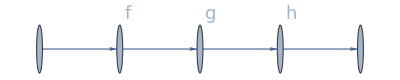

```mathematica
Graph[{1->2,2->3,3->4,4->5},VertexLabels->{2-> Style["f",18],3-> Style["g",18],4-> Style["h",18]}]
```

#### A single-layer chain

```mathematica
net=NetChain[{ElementwiseLayer[Tanh]}]
```

NetChain[<>]

```mathematica
net[{-1,0,1}]
```

{-0.761594,0.,0.761594}

This is simply applying the Tanh function to the data:

```mathematica
Tanh[{-1,0,1}]//N
```

{-0.761594,0.,0.761594}

#### Use special syntax for linear and elementwise layers

```mathematica
NetChain[{3,Tanh,4,Ramp,5}]
```

NetChain[<>]

## Stacking Layers: NetGraph

Non-cyclic graphs can also be used to represent the function f_w:

```mathematica
h(g(x),f(x))↦y
```

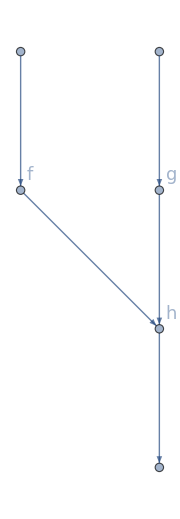

```mathematica
Graph[{1->2,3->4,2->5,4->5,5->6},VertexLabels->{2-> Style["f",18],4-> Style["g",18],5-> Style["h",18]},ImageSize->Small]
```

This is done in the Wolfram Language using NetGraph. NetGraph can be used to connect different layers to create a graphical neural network of any topology.

#### Constructing a chain using NetGraph

```mathematica
net=NetGraph[{2,Ramp,4,Ramp,8},{1->2->3->4->5}]
```

NetGraph[<>]

This is equivalent to a NetChain:

```mathematica
NetChain[{2,Ramp,4,Ramp,8}]
```

NetChain[<>]

#### Combining two layers

```mathematica
net=NetGraph[{Ramp,Tanh,Times,Plus},{1->2->3,1->3->4,2->4}]
```

NetGraph[<>]

```mathematica
data={-2,-1,0,1,2}
```

{-2,-1,0,1,2}

```mathematica
net[data]
```

{0.,0.,0.,1.52319,2.89208}

The seemingly complicated network structure is actually doing the following operation:

```mathematica
Tanh@Ramp@data*Ramp@data+Tanh@Ramp@data//N
```

{0.,0.,0.,1.52319,2.89208}

#### Concatenating output from intermediate layers

```mathematica
net=NetGraph[{Ramp,LogisticSigmoid,CatenateLayer[]},{1->2,{1,2}->3}]
```

NetGraph[<>]

#### NetChain can be used as a part of a NetGraph

```mathematica
chain=NetChain[{ElementwiseLayer[Ramp],ElementwiseLayer[LogisticSigmoid]}]
```

NetChain[<>]

```mathematica
NetGraph[{BatchNormalizationLayer[],chain},{1-> 2}]
```

NetGraph[<>]

## Stacking Layers: NetPort

NetPort represents the specified port for a layer in a NetGraph or similar structure.

### Creating a simple total NetGraph with two inputs

```mathematica
net=NetGraph[{Ramp,LogisticSigmoid,TotalLayer[]},{NetPort["Input1"]->1,NetPort["Input2"]->2,{1,2}->3}]
```

NetGraph[<>]

### Creating a net with two outputs

```mathematica
net=NetGraph[{Ramp,LogisticSigmoid},{1->2,1->NetPort["Output1"],2->NetPort["Output2"]}]
```

NetGraph[<>]

### Creating a net that explicitly computes a loss

In this example, the “shape” of the NetPort is determined by specifying the Input to scalar:

```mathematica
net=NetGraph[{ElementwiseLayer[Tanh],DropoutLayer[],MeanSquaredLossLayer[]},{1->NetPort[3,"Target"],2->NetPort[3,"Input"]}]
```

NetGraph[<>]

## Network Training I: Basic Theory

### Neural Networks Learn on Training Data

Neural networks are data-driven algorithms.

You can think of training data as implicitly specifying a function, where training “tunes” a net to approximate this function.

-Graphics-

### Basic Theory

Training a network finds a (local) optimum of the loss as a function of the learned parameters.

To train one parameter x, the error or cost function or loss ϵ of the network is computed on the entire training data. The chain rule is used to back-propagate the error ϵ through the network (full batch gradient descent).

Updating the parameter x→x- lr ∂x is known as gradient descent with learning rate lr.

The gradient ∂_w L determines the change of weights w in order to decrease L:

```mathematica
D[L(Subscript[f, w](x),y), w]= (∂L(Subscript[f, w](x),y))/(∂f) (∂Subscript[f, w](x))/(∂w)
```

Here is an example that shows how the error (cost function) is minimized with respect to the two parameters, using gradient descent:

```mathematica
f[x_,y_]:=x^4-2x^2+2y^4-2y^2+2x y 
pts = Reap[FindMinimum[x^4-2x^2+2y^4-2y^2+2x y ,{{x,-2.0},{y,-2.0}},Method-> "ConjugateGradient",StepMonitor:>Sow[{x,y}]]][[2,1]];
pts =Join[{{-2.0,-2.0}},pts];
table=Table[{pts[[i,1]],pts[[i,2]],f[pts[[i,1]],pts[[i,2]]]},{i,1,Length[pts]}];
Show[Plot3D[f[x,y],{x,-2,2.0},{y,-2,2.0},MeshFunctions->{#3&},Mesh->50, ColorFunction->"BeachColors"],Graphics3D[{Black,Thick,Line[table]}],Graphics3D[{PointSize[Large],Red,Point[table]}]]
```

-Graphics3D-

However, when the data is repetitive or too large, it is often more useful to train one parameter x; the error or loss or cost function ϵ of the network is computed on the subsets (or batches) of training data (mini-batch gradient descent/stochastic gradient descent):

```mathematica
w ↦w+Δw           Δw==-η ∑_(k∈B) ∂_w L(Subscript[f, w](Subscript[x, k]),Subscript[y, k])
```

The parameters of the network gradually converge on a local optimum, i.e. the error is minimized.

In practice, more complicated update schemes can be used by setting the Method option in NetTrain.

For training a neural network, the function NetTrain is used. NetTrain performs a lot of operations automatically: it will initialize the parameters in the layers and decide on the initial learning rate, the method for updating the parameters, the learning rate schedule, the batch size and the loss functions to use. However, you can modify the default options in NetTrain (please refer to the notes/reading materials at the end of the options section of NetTrain).

## The most important slide of all!

### LinearLayer

Mathematically, a linear layer is an affine transformation x→Ax+b, where A is the “weight matrix” and the vector b is the “bias vector”.

Every neuron of the top array is connected with the bottom array, resulting in n_in×n_out connections.

Hence, n_in×n_out weights and n_out biases have to be learned:

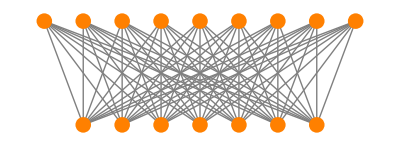

```mathematica
Block[
{h=4,r=0.3,layer0Pts,layer1Pts},
layer0Pts=Thread[{1.5 Range[0,8],h}];
layer1Pts=Thread[{1.5 Range[1,7],0}];
Graphics[
{{Gray,Outer[Line[{##}]&,layer0Pts,layer1Pts,1]},
{FaceForm[Orange],Map[Disk[#,r]&,layer0Pts],Map[Disk[#,r]&,layer1Pts]}
}
]
]
```

To understand what a linear layer does, it is easiest to construct a net with a single LinearLayer:

```mathematica
data={2,10,3};
layer=NetInitialize@LinearLayer[2,"Input"-> 3]
layer[data]
```

LinearLayer[<>]

{-7.73613,-2.60205}

```mathematica
linear[data_, weight_,bias_]:=Dot[weight,data]+bias
```

```mathematica
Normal@ NetExtract[layer,"Weights"]
```

{{-0.122887,-1.02034,0.904354},{-0.340604,-0.466215,0.913772}}

```mathematica
Normal@NetExtract[layer,"Biases"]
```

{0.,0.}

```mathematica
linear[data,Normal@ NetExtract[layer,"Weights"],Normal@NetExtract[layer,"Biases"]]
```

{-7.73613,-2.60205}

### ElementwiseLayer

The ElementwiseLayer applies a unary function f to every element of the input tensor:

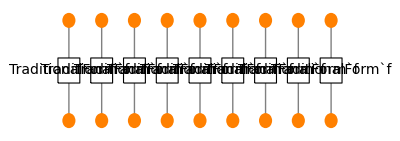

```mathematica
Block[
{h=4,r=0.3,layer0Pts,layer1Pts},
layer0Pts=Thread[{1.5 Range[0,8],h}];
layer1Pts=Thread[{1.5 Range[0,8],0}];
Graphics[
{{Gray,MapThread[Line[{##}]&,{layer1Pts,layer0Pts}]},
{FaceForm[White],EdgeForm[{Thin,Black}],Map[{Rectangle[#-1/2,#+1/2],Text[Style["TraditionalForm`f",14],#]}&,Thread[{1.5 Range[0,8],h/2}]]},
{FaceForm[Orange],Map[Disk[#,r]&,layer0Pts],Map[Disk[#,r]&,layer1Pts]}
}
]
]
```

The function f is referred to as the activation function in literature. Common choices for this so-called activation function are LogisticSigmoid, Tanh, Ramp (rectified linear unit, ReLU):

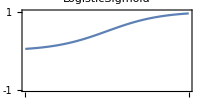
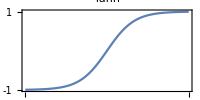
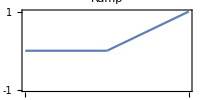

```mathematica
Row[Table[
{min,max}={-1,1}*If[f===Ramp,1,3];
Plot[f[x],{x,min,max},PlotLabel->f,ImageSize->200,Frame->True,PlotRange->{{min,max},{-1,1}},AspectRatio->0.5,FrameTicks->{{{-1,0,1},{}},{{min,0,max},{}}}],{f,{LogisticSigmoid,Tanh, Ramp}}], Spacer[50]]
```

```mathematica
elem=ElementwiseLayer[Tanh];
data=RandomReal[{0,10},10];
elem[data]
```

{0.967454,0.999999,0.985622,1.,0.968208,0.997003,0.999933,1.,1.,0.867371}

As you would expect, it applies Tanh to the data:

```mathematica
Tanh[data]
```

{0.967454,0.999999,0.985622,1.,0.968208,0.997003,0.999933,1.,1.,0.867371}

Without a nonlinearity, a stack of linear layers is equivalent to a single linear layer.

An ElementwiseLayer has no trainable parameters.

### SoftmaxLayer

The softmax classifier takes a vector as input and returns normalized exponential values as class probabilities. The element x_i in a vector is converted to e^x_i/∑_j e^x_j, and generally the innermost dimension is used as the normalization dimension:

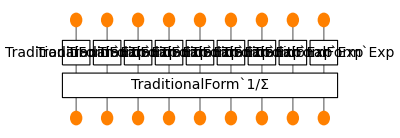

```mathematica
Block[
{h=4,r=0.3,layer0Pts,layer1Pts},
layer0Pts=Thread[{1.5 Range[0,8],h}];
layer1Pts=Thread[{1.5 Range[0,8],0}];
Graphics[
{{Gray,MapThread[Line[{##}]&,{layer1Pts,layer0Pts}]},
{FaceForm[White],EdgeForm[{Thin,Black}],Map[{Rectangle[#-{2/3,1/2},#+{2/3,1/2}],Text[Style["TraditionalForm`Exp",14],#]}&,Thread[{1.5 Range[0,8],2h/3}]],
Rectangle[{0,h/3}-{2/3,1/2},{12,h/3}+{2/3,1/2}],Text[Style["TraditionalForm`1/Σ",14],{6,h/3}]},
{FaceForm[Orange],Map[Disk[#,r]&,layer0Pts],Map[Disk[#,r]&,layer1Pts]}
}
]
]
```

Apply the SoftmaxLayer on a list of random data to get probabilistic interpretations. On a list:

```mathematica
data=RandomReal[{0,10},10];
{SoftmaxLayer[]@data,Total@SoftmaxLayer[]@data}
```

{{0.0153497,0.000795255,0.0093164,0.66332,0.00372489,0.0719289,0.00795535,0.0395192,0.0168919,0.171198},1.}

See what SoftmaxLayer is actually evaluating by using the functional approach:

```mathematica
fsoftmax[x_]:=N@Exp[x]/Total[Exp[x],{-1}];
{fsoftmax[data],Total@fsoftmax[data]}
```

{{0.0153497,0.000795255,0.0093164,0.66332,0.00372489,0.0719289,0.00795535,0.0395192,0.0168919,0.171198},1.}

## A Simple Classification Problem

### Gaussian

Two mostly separated Gaussians are a linear classification problem.

Create an artificial dataset from two normally distributed clusters:

```mathematica
makeCluster[class_,μ_,σ_]:=RandomVariate[BinormalDistribution[{μ,μ},{σ,σ},0],1000]->class;
clusters=makeCluster@@@{{Red,1,0.5},{Green,-1,0.5}};
```

Plot the dataset:

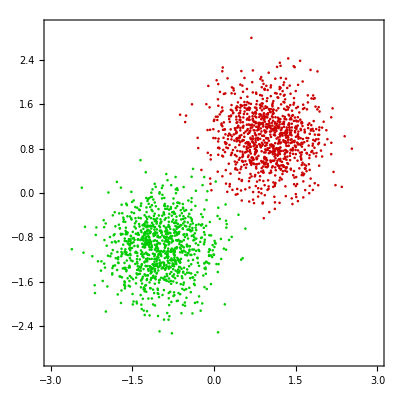

```mathematica
plot=ListPlot[Keys[clusters], PlotStyle->{RGBColor[0.8, 0., 0.],RGBColor[0., 0.8, 0.]},AspectRatio->1,Frame->True,PlotRange->{{-3,3},{-3,3}}]
```

The training data consists of rules mapping the point to the cluster it is in:

```mathematica
trainingData=Flatten[Thread/@clusters];
RandomSample[trainingData,6]
```

{{2.17656,1.52643}→RGBColor[1, 0, 0],{1.20102,0.226917}→RGBColor[1, 0, 0],{-0.895399,-1.38309}→RGBColor[0, 1, 0],{-0.0879822,-1.27189}→RGBColor[0, 1, 0],{-1.10265,-0.413658}→RGBColor[0, 1, 0],{0.579062,0.897132}→RGBColor[1, 0, 0]}

Create a net to compute the probability of a point lying in each cluster, using a "Class" decoder to classify the input as either Red or Green:

```mathematica
net=NetChain[{4 , (*First fully-connected layer*)
                          2,      (*Corresponds to 2 classes *)
                          SoftmaxLayer[]},"Input"->{2},"Output"->NetDecoder[{"Class",{Red,Green}}]]
```

NetChain[<>]

Train the net on the data:

```mathematica
trained=NetTrain[net,trainingData]
```

NetChain[<>]

Show the contours in feature space in which each class reaches a posterior probability of 0.75:

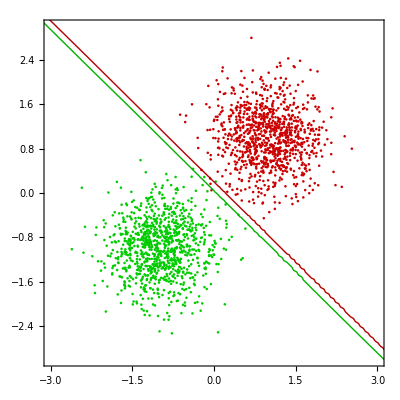

```mathematica
Show[plot,Quiet@Table[ContourPlot[trained[{x,y},{"Probability",color}]==0.75,{x,-5,5},{y,-5,5},ContourStyle->{Thick,Darker[color,.3]}],{color,{Red,Green}}]]
```

### XOR

The XOR classification problem is one of the simplest examples where linear classification fails.

Create an artificial dataset for XOR classification:

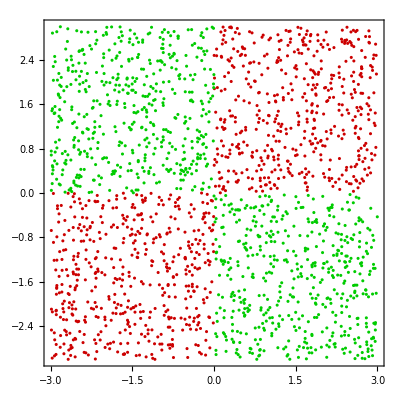

```mathematica
makeCluster[class_,r1_,r2_,r3_,r4_]:=RandomVariate[UniformDistribution[{{r1,r2}, {r3, r4}}],500]->class;
clusters=makeCluster@@@{{Red,0,3,0,3},{Red,-3,0,-3,0},{Green,-3,0,0,3},{Green,0,3,-3,0}};
plot=ListPlot[Keys[clusters], PlotStyle->{RGBColor[0.8, 0., 0.],RGBColor[0.8, 0., 0.],RGBColor[0., 0.8, 0.],RGBColor[0., 0.8, 0.]},AspectRatio->1,Frame->True,PlotRange->{{-3,3},{-3,3}}]
```

Create a net (with nonlinearity) to compute the probability of a point lying in each cluster, using a "Class" decoder to classify the input as either Red or Green:

```mathematica
trainingData=Flatten[Thread/@clusters];
net=NetChain[{10 , (*First fully-connected layer*)
                          Ramp, (*To provide the non-linearity required to draw the surfaces *)
                          2,      (*Corresponds to 2 classes*)
                          SoftmaxLayer[]},"Input"->{2},"Output"->NetDecoder[{"Class",{Red,Green}}]]
```

NetChain[<>]

Training and visualization:

NetChain[<>]

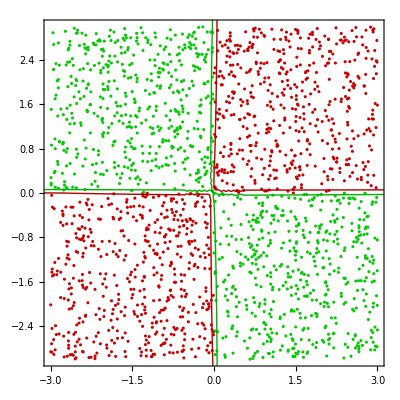

NetChain[<>]

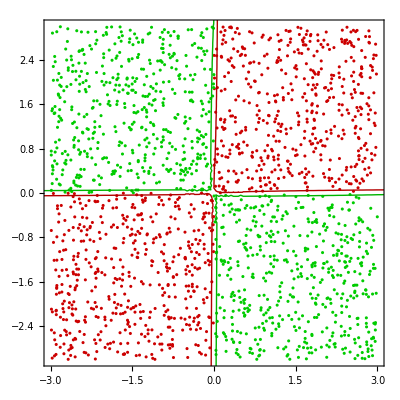

```mathematica
trained=NetTrain[net,trainingData]
Show[plot,Quiet@Table[ContourPlot[trained[{x,y},{"Probability",color}]==0.75,{x,-5,5},{y,-5,5},ContourStyle->{Thick,Darker[color,.3]}],{color,{Red,Green}}]]
```

## Exploration: Losses

Background

The loss layers specify the functional form of loss to be computed, which measures the compatibility between a prediction (e.g. the class scores in classification) and the actual value of the label. The data loss takes the form of an average over the data losses for every individual example. In the iteration of training the network, this explicit loss function is minimized by tuning the parameters (via back propagation). When a loss layer is chosen automatically for a port, the loss layer to use is based on the layer within the net whose output is connected to the port. For SoftmaxLayer and LogisticSigmoid, CrossEntropyLossLayer is chosen, for non-loss layers, MeanSquaredLossLayer is chosen. If a loss layer is specified, it is used unchanged. You can also specify custom losses using the option LossFunction.

### Examples of Some Implemented Loss Layers

MeanSquaredLossLayer: represents a loss layer that computes the mean squared difference between the "Input" port and "Target" port (Gaussian type used for regression problem):

```mathematica
data=<|"Input"-> {1,2,3},"Target"->{3,2,1}|>;
MeanSquaredLossLayer[][data]
meanSquaredLoss=N[Mean[Flatten[(#Input-#Target)^2]]]&; 
meanSquaredLoss[data]//N
```

2.66667

2.66667

CrossEntropyLossLayer: represents a net layer that computes the information-theoretic distance by comparing probabilities with specified target values (used for classification problem):

```mathematica
data=<|"Input"-> {0.1,0.2,0.7},"Target"->{0.12,0.3,0.6}|>;
CrossEntropyLossLayer["Probabilities"][data]
ceLoss=-Total[#Target*Log@#Input]&;
ceLoss[data]
```

0.973147

0.973147

Implement a MeanSquareAbsoluteLoss using ThreadingLayer.

Hint: Refer to the documentation of ThreadingLayer.

```mathematica
meansquareloss=NetGraph[{ThreadingLayer[(#1-#2)^2&]},{{NetPort["Input"],NetPort["Target"]}->1},"Input"->"Real"]
```

NetGraph[<>]

Perform linear regression using the created layer on the following layer: data={1→1, 2→2, 3→3, 4→9, 5→5}.

```mathematica
data={1->1,2->2,3->3,4->9,5->5};
trained=NetTrain[LinearLayer[],data,LossFunction->meansquareloss,MaxTrainingRounds->10000]
```

LinearLayer[<>]

Plot the solution.

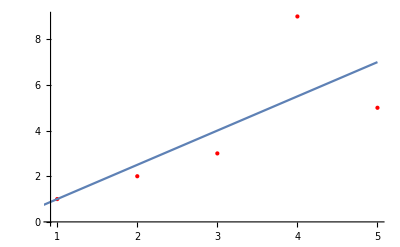

```mathematica
dataPlot=ListPlot[List@@@data,PlotStyle->{Red,PointSize[Medium]}];
Show[dataPlot,Plot[trained[x],{x,0,5}]]
```

Do a validation of your implementation by comparing the solution with the implemented MeanSquaredLossLayer[].

```mathematica
{net1,net2}=NetTrain[LinearLayer[],data,LossFunction->#1,MaxTrainingRounds->10000]&/@{MeanSquaredLossLayer[],meansquareloss};
```

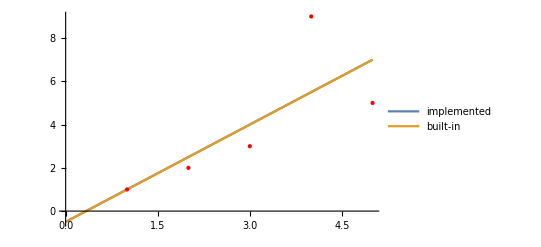

```mathematica
Show[
Plot[{Legended[net1[x],"implemented"],Legended[net2[x],"built-in"]},{x,0,5},PlotRange->All],
dataPlot]
```

You can further repeat the same experiment with the functional form of MeanAbsoluteLossLayer[].

## Convolution Layers

### Convolution Layer

A ConvolutionLayer will apply convolution on a tensor, usually performing a downsampling/ filtering operation. It takes a kernel (square or rectangular), stride and padding to create the output. This is the core building block of convolution neural networks (CNNs). CNNs often have several levels of convolution layers, which pick up patterns at different levels of detail (recognize large structures, then smaller patterns, etc.). Conceptually, you replace a section of pixels in an image with a weighted average of their values. The weights are the parameters of the layer.

-Graphics-

The following function computes the size of the non-channel dimensions, given the input size and parameters:

```mathematica
outputconv[inputSize_List,kernSize_,stride_,pad_,dilate_]:=Floor[(inputSize+2*pad-(dilate*(kernSize-1)+1))/stride]+1
```

### Deconvolution Layer

Unlike what the name suggests, a DeconvolutionLayer will not apply a deconvolution operator on a tensor, but will perform an upsampling operation. It is sometimes called transposed convolution or convolution with fractional strides.

The following function computes the size of the non-channel dimensions, given the input size and parameters:

```mathematica
outputdeconv[inputSize_List,kernSize_,stride_,pad_]:=(stride*(inputSize-1)+kernSize-2*pad)
```

### Pooling Layer

A form of nonlinear downsampling, often used in CNNs in between convolution layers. The functions that could be used are Max, Mean, Total:

-Graphics-

The following function computes the size of the non-channel dimensions, given the input size and parameters:

```mathematica
outputpool[inputSize_List,kern_,stride_,pad_]:=
Floor[(inputSize+2*pad-kern)/stride]+1
```

## Exploration: Multiple-Choice Questions

The output size of a PoolingLayer of input of size {256,256}, a kernel size of {2,3}, a stride of 2, a dilation factor of {3,4} and a padding size of {1,2}:

a) {129, 127}
b) {128, 126}
c) {127, 129}
d) {126, 128}

The output size of a ConvolutionLayer of input of size {256,256}, a kernel size of {2,3}, a stride of 2, a dilation factor of {3,4} and a padding size of {1,2}:

a) {129, 127}
b) {128, 126}
c) {127, 129}
d) {126, 128}

The output size of a DeconvolutionLayer input of size {256,256}, a kernel size of {2,3}, a stride of 2, a dilation factor of {3,4} and a padding size of {1,2}:

a) {507, 239}
b) {509, 237}
c) {507, 237}
d) {509, 239}

## A Simple Convolution Network: LeNet

### Constructing the Network

```mathematica
lenet=NetChain[{
(*STEP 1: FEATURE EXTRACTION*)
       (*FIRST CONVOLUTION BLOCK*) 
ConvolutionLayer[20,5],(*first convolution => 20 feature images*)
Ramp,  (*activation function (ReLU) => non-linearity, sparsity*)
(*FIRST POOLING BLOCK*)
PoolingLayer[2,2],  (*max pooling => downsampling*)
(*SECOND CONVOLUTION BLOCK*)
ConvolutionLayer[50,5],(*second convolution => 50 feature images*)
Ramp,
(*SECOND POOLING BLOCK*)
PoolingLayer[2,2],
FlattenLayer[],(*flattening => images to vector*)
(*STEP 2: COMPUTING CLASS PROBABILITY*)
(*FULLY-CONNECTED BLOCK 1*)
500,(*first fully connected layer => feature vector from image features*)
Ramp,
(*FULLY-CONNECTED BLOCK 2*)
10,(*second fully connected layer => class prediction*)
(*PROBABILITY COMPUTATIONS*)
SoftmaxLayer[]},(*normalization*)
"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}], (*encoder => image to tensor*)"Output"->NetDecoder[{"Class",Range[0,9]}]  (*decoder => tensor to class*)
]
```

NetChain[<>]

### Network Data

In this example, LeNet is trained on the handwritten digits from the MNIST database. In the Wolfram Language database, the digits are classified into training and test datasets. Get them:

```mathematica
trainingData=ResourceData[ResourceObject["MNIST"],"TrainingData"];
testData=ResourceData[ResourceObject["MNIST"],"TestData"];
```

### Network Training II: Various Options

The network will now be trained on the training data (with different options to make the process faster).

If you perform a simple NetTrain, you will see that the training takes approximately six minutes:

```mathematica
trained=NetTrain[lenet,trainingData,All]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:9380  rounds:10  time:3.0min  examples/s:3290
data | ,,  training examples:60000  processed examples:600320  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:7.×10^-3  error:0.218%
 | 
 | ]

Try to improve the speed by changing the number of MaxTrainingRounds and setting it to 2 (reduces training time by a factor of 5) and changing the BatchSize, which in turn improves the number of inputs per second:

```mathematica
trained=NetTrain[lenet,trainingData,All,MaxTrainingRounds->2,BatchSize->512 ]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:236  rounds:2  time:40s  examples/s:3059
data | ,,  training examples:60000  processed examples:120832  skipped examples:0
method | ,,  ADAMoptimizer  batch size512CPU
round | ,,  loss:7.64×10^-2  error:2.34%
 | 
 | ]

```mathematica
trainedNet = trained["TrainedNet"]
```

NetChain[<>]

Finally, if you have a GPU, the training goes much faster; in this case the training completes in 20 s:

WARNING: DO NOT EVALUATE!

```mathematica
trained=NetTrain[lenet,trainingData,All,MaxTrainingRounds->2,BatchSize->512,TargetDevice->"GPU" ]
```

NetTrain::trgdevegpu: TargetDevice -> GPU could not be used; a supported NVIDIA GPU was not found. If you are using an external GPU, ensure it is attached and recognized by your OS; restarting your system may help. Additionally, check that you are using the latest drivers from http://www.nvidia.com/object/mac-driver-archive.html.

$Failed

## Exploration: Debugging

Identify the mistake in the code:

```mathematica
lenet2=NetChain[{ConvolutionLayer[60,5],Ramp,PoolingLayer[3,3], ConvolutionLayer[60,5],Ramp,PoolingLayer[2,2],FlattenLayer[],500,Ramp,12,SoftmaxLayer[]},
"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}], "Output"->NetDecoder[{"Class",Range[0,9]}]  
]
```

NetChain::tyfail2: Inferred inconsistent dimensions for output of layer 11 (a length-10 vector of real numbers versus a length-12 vector of real numbers).

$Failed

## LeNet: Properties and Export

### Obtaining Different Properties

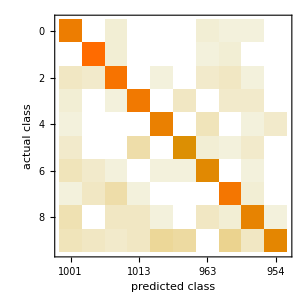
Classifier Measurements
Classifier method | Net
Number of test examples | 10000
Accuracy | (98.260.13) %
Accuracy baseline | (11.350.32) %
Geometric mean of probabilities | 0.946 ± 0.0031
Mean cross entropy | 0.0554 ± 0.0033
Single evaluation time | 2.41 ms/example
Batch evaluation speed | 4.27 examples/ms
-Graphics- |

```mathematica
cm=ClassifierMeasurements[trainedNet,testData]
```

```mathematica
cm["ConfusionMatrixPlot"]
```

-Graphics-

```mathematica
cm["Accuracy"]
```

0.9826

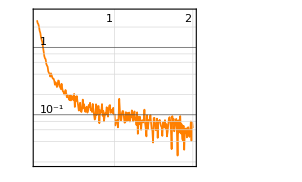
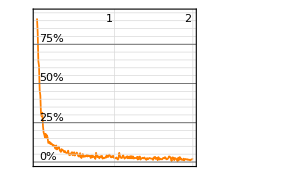
<|Loss→ | rounds
loss | -Graphics-,ErrorRate→ | rounds
error rate | -Graphics-|>

```mathematica
trained["FinalPlots"]
```

### Exporting a Trained Net

```mathematica
Export["testnet.wlnet",trainedNet]
```

testnet.wlnet

```mathematica
trained=Import["testnet.wlnet"]
```

NetChain[<>]

```mathematica
cm=ClassifierMeasurements[trained,testData]
```

Classifier Measurements
Classifier method | Net
Number of test examples | 10000
Accuracy | (98.260.13) %
Accuracy baseline | (11.350.32) %
Geometric mean of probabilities | 0.946 ± 0.0031
Mean cross entropy | 0.0554 ± 0.0033
Single evaluation time | 2.52 ms/example
Batch evaluation speed | 4.29 examples/ms
-Graphics- |

```mathematica
cm["Accuracy"]
```

0.9826

## Exploration: Regularization and Network Training

Generate noisy data by adding random noise, with an underlying Gaussian distribution, and visualize it.

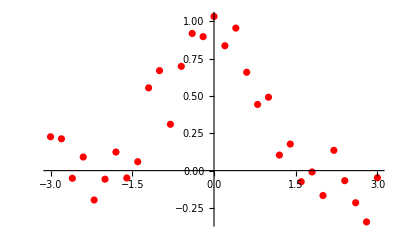

```mathematica
data=Table[x->Exp[-x^2]+RandomVariate[NormalDistribution[0,.15]],{x,-3,3,.2}];
plot=ListPlot[List@@@data,PlotStyle->Red]
```

Use a low “capacity” perceptron network for training.

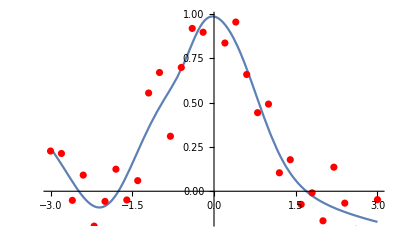

```mathematica
net=NetChain[{5,Tanh,1},"Input"->"Scalar","Output"->"Scalar"];
net3=NetTrain[net,data,Method->"ADAM"];
Show[Plot[net3[x],{x,-3,3}],plot]
```

Train the network with a “large” capacity perceptron model.

```mathematica
net=NetChain[{150,Tanh,150,Tanh,1},"Input"->"Scalar","Output"->"Scalar"];
net1=NetTrain[net,data,Method->"ADAM"];
```

Visualize the training to see how the model overfits to the noise.

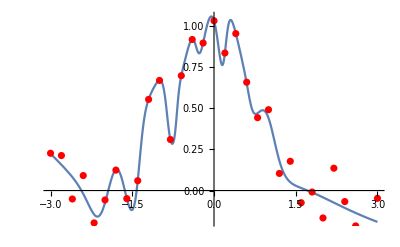

```mathematica
Show[Plot[net1[x],{x,-3,3}],plot]
```

Now add a "Regularization" parameter to NetTrain to prevent overfitting.

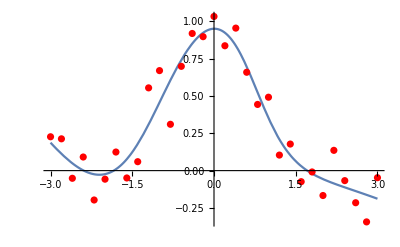

```mathematica
net2=NetTrain[net,data,Method->{"ADAM","L2Regularization"->0.001}];
Show[Plot[net2[x],{x,-3,3}],plot,PlotRange->All]
```

Stop the training immediately and visualize the results.

```mathematica
net=NetChain[{150,Tanh,150,Tanh,1},"Input"->"Scalar","Output"->"Scalar"];
net3=NetTrain[net,data,Method->"ADAM"];
Show[Plot[net3[x],{x,-3,3}],plot]
```

-Graphics-

Do it programmatically using the TrainingStoppingCriterion.

```mathematica
net4=NetTrain[net,data,Method->"ADAM",TrainingStoppingCriterion-><|"Criterion"->"Loss", "AbsoluteChange"->0.00001|>];
Show[Plot[net3[x],{x,-3,3}],plot]
```

NetTrain::novalidation: No validation set provided, defaulting to training set for stopping criterion.

-Graphics-

An alternate approach is to use DropoutLayer. It represents a net layer that sets its input elements to zero with probability 0.5 during training and is a commonly used form of regularization.

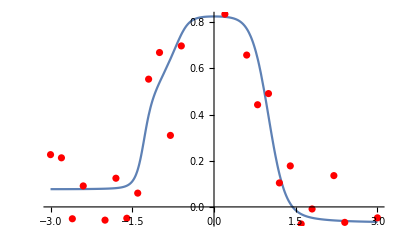

```mathematica
net=NetChain[{150,Tanh,DropoutLayer[0.8],150,Tanh,DropoutLayer[0.8],1},"Input"->"Scalar","Output"->"Scalar"];
net3=NetTrain[net,data,Method->"ADAM"];
Show[Plot[net3[x],{x,-3,3}],plot]
```

## Why Use the Wolfram Language?

Polished high-level framework without performance sacrifices

User-friendly

Interactive

Automatic support of variable-length sequences

Repository of pretrained networks

Easy to do "network surgery"

Pre- and post-processing in the network

Check of constraints, human-readable error messages

Performance

MXNet backend

Multi-GPU and Tensor Core support (mixed-precision)

Documentation

https://reference.wolfram.com/language/tutorial/NeuralNetworksOverview.html

Wolfram Support

CloudDeploy

## Additional Notes: Optimization and Network Training (IV)

### Vanilla update

Basic method (not in the Wolfram Language)

Update parameters in the negative direction of the gradient.

Parameters x and the gradient dx, form used is: x→ x- lr ∂x

### Momentum update

Basic method (not in the Wolfram Language)

Better convergence for rates on deep networks

The update has the form: 
v = μ * v -lr *dx  # integrate velocity
x += v  # integrate position
Here you see an introduction of a variable, v, i.e. the velocity that is initialized at zero, and an additional hyperparameter μ, which is entered in the Wolfram Language (as Momentum) and related to viscosity in physical systems.

### Nesterov momentum update

SGD in the Wolfram Language

In this method of updating the momentum, you are looking one step ahead, and as a result you have a little bit better guess for the step.
v_prev = v # back this up
v = μ * v - lr * dx # velocity update stays the same
x += - μ * v_prev + (1 + μ) * v # position update changes form

-Graphics-

### RMS-Prop

RMSProp in the Wolfram Language

The update has the form
cache += Beta* cache + (1 - Beta) * dx**2
x += - Beta * dx / (Sqrt(cache) + ϵ)
Here, Beta is a hyperparameter and typical values are [0.9, 0.99, 0.999]. The smoothing term ϵ (~1e-4 to 1e-8) avoids division by zero.

-Graphics-

### Adam

Adam in the Wolfram Language

The update has the form
m = Beta1*m + (1-Beta1)*dx
v = Beta2*v + (1-Beta2)*(dx**2)
x += - lr * m / (Sqrt(v) + ϵ)

https://arxiv.org/pdf/1412.6980.pdf
Recommended values in the paper are ϵ = 1 e - 8, beta1 = 0.9, beta2 = 0.999.

-Graphics-

## Additional Notes: Initialization and Network Training (IV)

NetIntialize[net] gives a net in which all uninitialized learnable parameters in net have been given initial values. By default, all methods initialize bias vectors to zero.

-Graphics-

Random : Weights should be very close to zero, but not identically zero. As a solution, it is common to initialize the weights of the neurons to small numbers, so that they are updated differently and form different parts of the full network. You can separately initialize the weight matrices and vectors using the suboptions present.

-Graphics-

W ∝ RandomVariate[NormalDistribution[0, 0.1/0.01]]

Identity: The distribution of the outputs from a randomly initialized neuron has a variance that grows with the number of inputs. This variance of each neuron’s output can be normalized to 1, by scaling its weight vector by the square root of the number of inputs. This is done by initializing the net using the "Identity" method,  which results in a net that attempts to preserve the components of tensors as they pass through linear layers.

W ∝ RandomVariate[UniformDistribution[-1/√n_in,1/√n_in]]

Xavier: Another way of scaling the variance can be done by choosing weights to preserve the variance of arrays when propagated through various layers, following the method introduced by Xavier Glorot et al. (2014).

RandomVariate[UniformDistribution[-r,r]] ; r∝√(6/(n_in+n_out))

http://proceedings.mlr.press/v9/glorot10a/glorot10a.pdf (Xavier et.al)

Kaiming: Yet another way of scaling the variance can be done by choosing weights to preserve the variance of arrays when propagated through various layers, following the method introduced by Kaiming He et al. (2015).

RandomVariate[UniformDistribution[-r,r]] ; r=√(2/n_in)

https://arxiv.org/pdf/1502.01852v1.pdf (He. et.al)

Orthogonal: First initialize the weight matrix, then perform SingularValueDecomposition. 
W_init = RandomReal[{0,0.1}, {n,m}]; 
{W_fin,w,v} = SingularValueDecomposition[W_init ]; W_fin is your required weight

## References and Glossary

Guide page: NeuralNetworks

Wolfram Neural Net Repository™

AbsoluteTiming | AspectRatio | BatchNormalizationLayer | BatchSize | BinormalDistribution
CatenateLayer | ClassifierMeasurements | Classify | ColorSpace | ContourPlot
ContourStyle | Cos | CrossEntropyLossLayer | Darker | DeleteMissing
Dimensions | Dot | ElementwiseLayer | Epilog | ExampleData
Exp | False | Flatten | Frame | FrameLabel
FrameTicks | GrayLevel | Green | ImageDimension | Keys
List | ListLinePlot | ListPlot | LogisticSigmoid | MaxTrainingRounds
Mean | MeanAbsoluteLossLayer | MeanInputsPerSecond | MeanSquaredLossLayer | Method
N | NetChain | NetDecoder | NetEncoder | NetExtract
NetGraph | NetInitialize | NetPort | None | NormalDistribution
Plot | PlotLegends | PlotRange | PlotRangePadding | PlotStyle
Plus | Quantity | Quiet | RandomReal | RandomSample
RandomVariate | Range | Show | SoftmaxLayer | Table
TakeDrop | Tanh | Target | TargetDevice | Text
Thick | Thread | Times | Total | TotalLayer
TrainingProgressReporting | True | UniformDistribution | UnitVector |